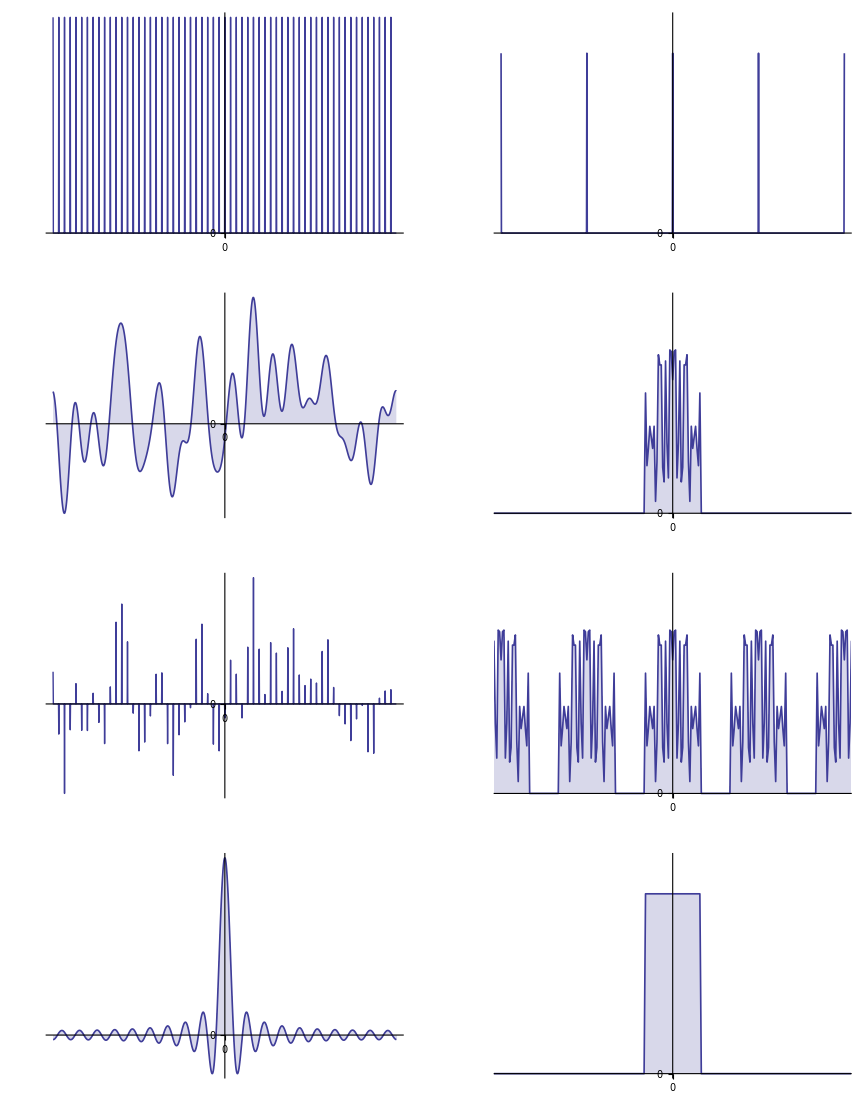

```mathematica
n = 1200;
b = 20;
step = n/(b*3);
Window = Table[If[i<b || i>n-b,1,0],{i,0,n-1}];
Signal = InverseFourier[Fourier[RandomReal[{-1,1},n]]*Window];
FSignal = Fourier[Signal];
Shah = Table[If[Mod[i,step] == 0,1,0],{i,0,n-1}];
FShah = Table[If[Mod[i,n/step] == 0,1,0],{i,0,n-1}];
FFTPlot[a_]:= ListPlot[Table[{(i-n/2)/n,Abs[a[[1+Mod[i+n/2,n]]]]},{i,0,n-1}],PlotRange->{{-0.1,0.1},{0,1.2}},Joined->True,Axes->{True,False},Ticks->{{0},{0}},Filling->Bottom,PlotStyle->{Thickness[0.003]}];
FShahPlot[a_]:= ListPlot[Table[{i,If[Mod[i,250] == 0,1,0]},{i,-500,500}],PlotRange->{{-500,500},{0,1.2}},Joined->True,Axes->{True,False},Ticks->{{0},{0}},Filling->Bottom,PlotStyle->{Thickness[0.003]}];
FFTFillPlot[a_]:= ListPlot[Table[{(i-n/2)/n,Abs[a[[1+Mod[i+n/2,n]]]]},{i,0,n-1}],PlotRange->{{-0.1,0.1},{0,1.2}},Filling->Bottom,Joined->True,PlotStyle->{Thickness[0.003]}];
ShiftPlot[a_]:= ListPlot[Table[{(i-n/2)/n,a[[1+Mod[i+n/2,n]]]},{i,0,n-1}],PlotRange->All,Axes->{True,False},Ticks->{{0},{0}},Joined->True];
ShiftFillPlot[a_]:= ListPlot[Table[{(i-n/2)/n,a[[1+Mod[i+n/2,n]]]},{i,0,n-1}],PlotRange->{Min[a],Max[a]},Axes->{True,False},Ticks->{{0},{0}},Joined->True,Filling->Axis,PlotStyle->{Thickness[0.003]}];
SampSignal = Signal*Shah;
SampFSignal =ListConvolve[FSignal,FShah,1];
NormalPlot[a_]:= ListPlot[a,Filling->Bottom,Joined->True,PlotRange->{0,1},Axes->{True,False},Ticks->None,PlotStyle->{Thickness[0.1]}]
SetDirectory["/home/filipe/Documents/PhD-Thesis/"];
Export["Signal.pdf",ShiftFillPlot[Signal]];
Export["FSignal.pdf",FFTPlot[FSignal]];
Export["Shah.pdf",ShiftPlot[Shah]];
Export["FShah.pdf",FShahPlot[FShah]];
Export["SampSignal.pdf",ShiftPlot[SampSignal]];
Export["FSampSignal.pdf",FFTPlot[SampFSignal]];
Export["FWindow.pdf",ShiftFillPlot[Re[Fourier[Window]]Sqrt[n]/(b*2-1)]];
Export["Window.pdf",FFTPlot[Window]];
GraphicsArray[{{ShiftPlot[Shah],FShahPlot[FShah]},{ShiftFillPlot[Signal],FFTPlot[FSignal]},{ShiftPlot[SampSignal],FFTPlot[SampFSignal]},{ShiftFillPlot[Re[Fourier[Window]]Sqrt[n]/(b*2-1)],FFTPlot[Window]}}]
```

```mathematica
ShiftPlot[Shah]
```

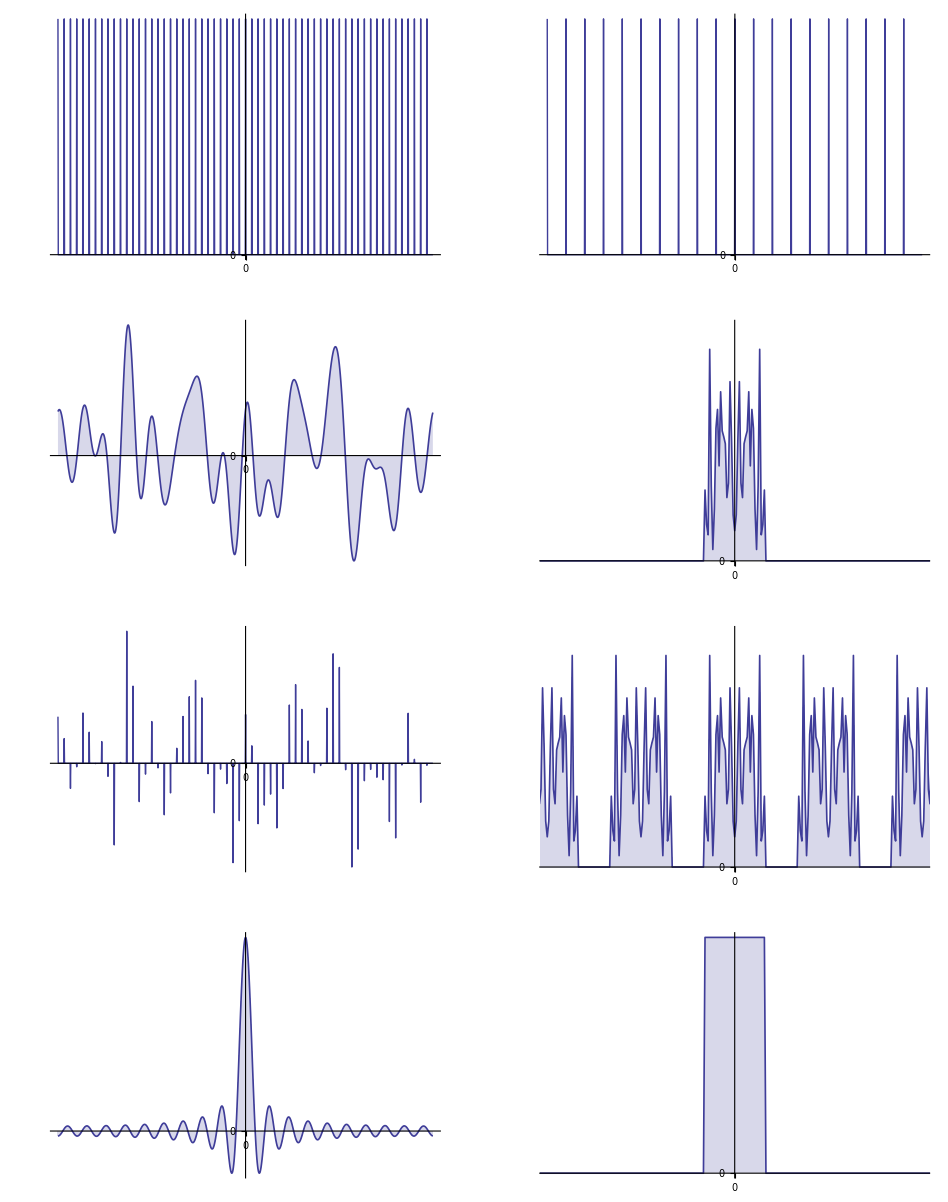

```mathematica
GraphicsArray[{{ShiftPlot[Shah],ShiftPlot[FShah]},{ShiftFillPlot[Signal],FFTPlot[FSignal]},{ShiftPlot[SampSignal],FFTPlot[SampFSignal]},{ShiftFillPlot[Re[Fourier[Window]]Sqrt[n]/(b*2-1)],FFTPlot[Window]}}]
```